```mathematica
img=Import["C:\\Users\\Andy\\Google Drive\\HUwebMMA\\IMG_3582.JPG"]
```

-Graphics-

```mathematica
imgsmall=ImageResize[img,300]
```

-Graphics-

```mathematica
dc=DominantColors[imgsmall,10,{"Color","CoverageImage"}]
```

{{RGBColor[0.050068314765557044, 0.04918020898556424, 0.04639790231850124],-Graphics-},{RGBColor[0.3756327299804813, 0.3926304661643763, 0.37771817097414023],-Graphics-},{RGBColor[0.5065146587223123, 0.4783340832602439, 0.4368758596308932],-Graphics-},{RGBColor[0.27457397758748114, 0.23891280087297528, 0.2135053398869901],-Graphics-},{RGBColor[0.40110870177291735, 0.3547932912668541, 0.3013858308709709],-Graphics-},{RGBColor[0.9215813401744637, 0.8193680158482287, 0.715779804365516],-Graphics-},{RGBColor[0.762220665278892, 0.6472747538039935, 0.5451235300146431],-Graphics-},{RGBColor[0.14980003890925545, 0.14120086689753328, 0.1373510124745146],-Graphics-},{RGBColor[0.6433009208314697, 0.6273084751270086, 0.5923989985867842],-Graphics-},{RGBColor[0.28291905915859034, 0.4669969341190691, 0.5086792808047683],-Graphics-}}

```mathematica
bluemask=%[[-1,2]]
```

-Graphics-

```mathematica
Manipulate[ImageAdd[imgsmall,ImageMultiply[bluemask,n]],{n,0,1}]
```

```mathematica
ImageMultiply[bluemask,dc[[2,1]]]
```

-Graphics-

```mathematica
withoutblue=ImageAdd[ImageMultiply[imgsmall,ColorNegate[bluemask]],ImageMultiply[bluemask,dc[[2,1]]]]
```

-Graphics-

```mathematica
GraphicsRow[{imgsmall,withoutblue}]
```

-Graphics-

```mathematica
GaussianFilter[imgsmall,10]
```

-Graphics-

```mathematica
smalldotsbin=Binarize[ImageSubtract[withoutblue,GaussianFilter[withoutblue,10]]]
```

-Graphics-

```mathematica
{{152.,200.99999999999997},{200.,283.}}
```

```mathematica
centerandedge={{152.,200.99999999999997},{200.,283.}};
rad=Norm[centerandedge[[1]]-centerandedge[[2]]]
```

95.0158

```mathematica
inside[{x_,y_}]:=Norm[centerandedge[[1]]-{x,y}]<rad
```

```mathematica
inside[{500,500}]
```

False

```mathematica
mcwhite=MorphologicalComponents[smalldotsbin];
Colorize[mcwhite]
```

-Graphics-

```mathematica
scsmall=SelectComponents[mcwhite,{"Centroid","Area"},inside[#1]&&#2<20&];
```

```mathematica
Colorize[scsmall]
```

-Graphics-

```mathematica
Manipulate[ImageAdd[imgsmall,ImageMultiply[Colorize[scsmall],n]],{n,0,1}]
```

```mathematica
mcblue=MorphologicalComponents[bluemask];
scblue=SelectComponents[mcblue,{"Centroid","Area"},inside[#1]&&#2<200&];
Colorize[scblue]
```

-Graphics-

```mathematica
ImageAdd[imgsmall,Colorize[scblue]]
```

-Graphics-

```mathematica
giflist={imgsmall,ImageAdd[ImageMultiply[imgsmall,0.5],Colorize[scblue]],imgsmall,ImageAdd[ImageMultiply[imgsmall,0.5],Colorize[scsmall]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["C:\\Users\\Andy\\Google Drive\\HUwebMMA\\bacteria.gif",giflist,"DisplayDurations"->1]
```

C:\Users\Andy\Google Drive\HUwebMMA\bacteria.gif

```mathematica
bluemask
```

-Graphics-

```mathematica
bmmd=ImageAdjust[MaxDetect[DistanceTransform[bluemask]]]
```

-Graphics-

```mathematica
ImageAdd[ImageMultiply[bluemask,0.5],ImageMultiply[bmmd,Red]]
```

-Graphics-

```mathematica
whitesize=ComponentMeasurements[scsmall,"Area"][[All,2]];
bluesize=ComponentMeasurements[scblue,"Area"][[All,2]];
```

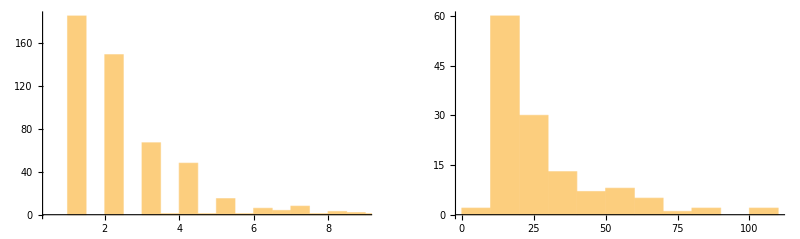

```mathematica
GraphicsRow[Histogram/@{whitesize,bluesize}]
```

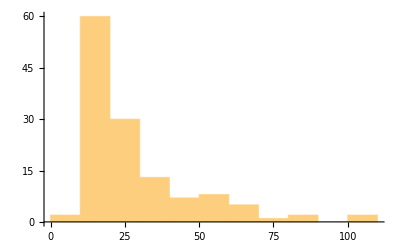

```mathematica
Histogram[bluesize]
```

```mathematica
Length[bluesize]
```

133

```mathematica
Length[whitesize]
```

500